```mathematica
Bifurfaction curves z vs q
```

Bifurfaction curves q vs z

```mathematica
GE1[q_, p_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*Boole[m>k*r], {m, 0, k-1}]*Sum[PDF[BinomialDistribution[k,p],w]*Boole[w>k*r], {w, 0, k}],{k,1,100}]
```

ⅇ^-z Boole[0>r] ((1-p) Boole[0>r]+p Boole[1>r])+98+(ⅇ^-z z^99 (1) ((1-p)^100 Boole[0>100 r]+100 (1-p)^99 p Boole[1>100 r]+98+p^100 Boole[100>100 r]))/(933262154439441526816992388562667004907159682643816214685929638952239761565182862536979208272237582511852109168640000000000000000000000)
 |  |  |  |

```mathematica
GN1[q_, p_, z_, r_] = (Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*Boole[m>k*r], {m, 0, k-1}],{k,1,100}])* (Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,p],w]*Boole[w>k*r], {w, 0, k}],{k,1,100}])
```

(ⅇ^-z Boole[0>r]+1+97+(ⅇ^-z z^99 ((1-q)^99 Boole[0>100 r]+99 (1-q)^98 q Boole[1>100 r]+96+99 (1-q) q^98 Boole[98>100 r]+q^99 Boole[99>100 r]))/933262154439441526816992388562667004907159682643816214685929638952175999932299156089414639761565182862536979208272237582511852109168640000000000000000000000) (1)
 |  |  |  |

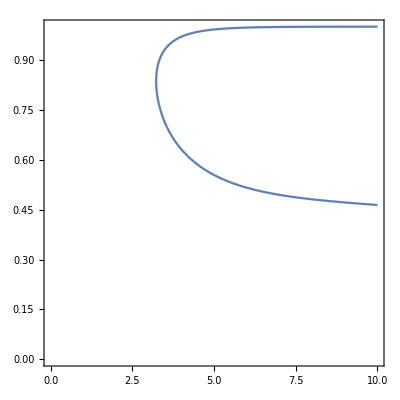

```mathematica
ContourPlot[GE1[q, q, z, 0.371]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

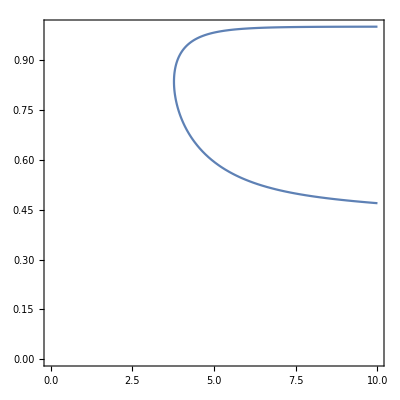

```mathematica
ContourPlot[GN1[q, q, z, 0.371]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

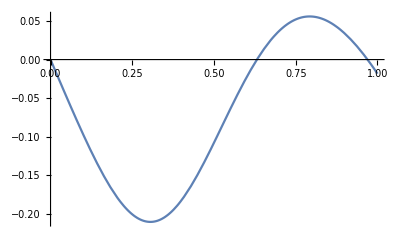

```mathematica
Plot[GE1[q, q, 4, 0.371]-q , {q, 0, 1}]
```

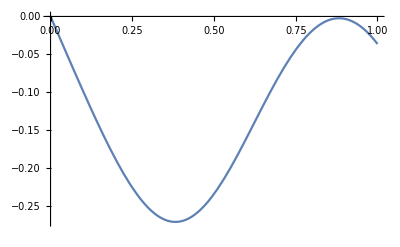

```mathematica
Plot[GN1[q, q, 4, 0.4]-q , {q, 0, 1}]
```

```mathematica
GE1gauss[q_, p_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]
```

1/2 ⅇ^-z Erfc[3.53553 r] (1/2 p Erfc[3.53553 (-1+r)]+1/2 (1-p) Erfc[3.53553 r])+ⅇ^-z z (1/2 p^2 Erfc[3.53553 (-1+r)]+(1-p) p Erfc[3.53553 1]+1/2 (1-p)^2 Erfc[3.53553 r]) (1/2 q Erfc[3.53553 (-1/2+r)]+1/2 (1-q) Erfc[3.53553 r])+96+1+(ⅇ^-z z^99 (1) (1/2 q^99 Erfc[3.53553 (-99/100+r)]+99/2 (1-q) q^98 Erfc[3.53553 (-49/50+r)]+4851/2 (1-q)^2 q^97 Erfc[3.53553 (-97/100+r)]+95+99/2 (1-q)^98 q Erfc[3.53553 (-1/100+r)]+1/2 (1-q)^99 Erfc[3.53553 r]))/933262154439441526816992388562667004907159682643816214685929638952175999932299156089414639761565182862536979208272237582511852109168640000000000000000000000
 |  |  |  |

```mathematica
GN1gauss[q_, p_, z_, r_] = (Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}])* (Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]);
```

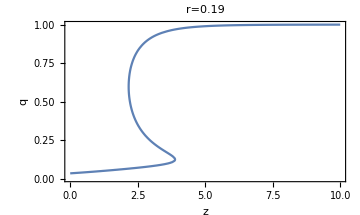

```mathematica
ContourPlot[GE1gauss[q, q, z, 0.19]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4, FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.19],LabelStyle->{GrayLevel[0]}, ImageSize->{360,215},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r019.eps",%159,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r019.eps

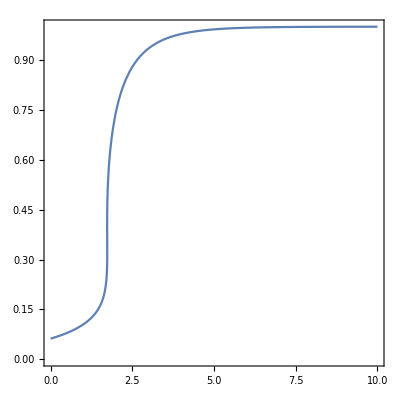

```mathematica
ContourPlot[GE1gauss[q, q, z, 0.15]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

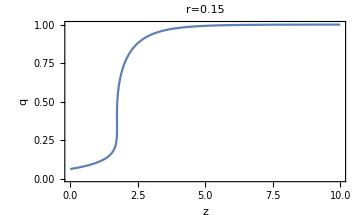

```mathematica
Show[%153,FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.15],LabelStyle->{GrayLevel[0]}, ImageSize->{360,215},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r015.eps",%156,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r015.eps

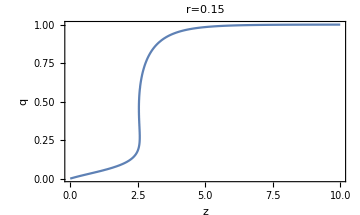

```mathematica
Show[%141,ImageSize->{360,215},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qz_r015.eps",%142,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qz_r015.eps

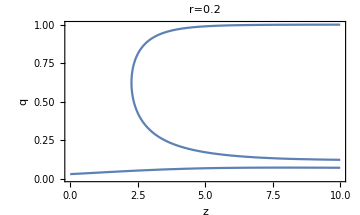

```mathematica
ContourPlot[GE1gauss[q, q, z, 0.2]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4, ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.2],LabelStyle->{GrayLevel[0]}]
```

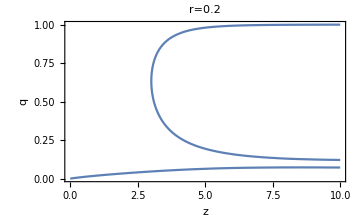

```mathematica
Show[%134,ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r02.eps",%155,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_edge_qz_r02.eps

```mathematica
ContourPlot[GE1gauss[q, q, z, 0.371]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

```mathematica
CountRoots[Ggauss[q, 4, 0.371]-q, {q, 0, 1}]
```

```mathematica
CascadeEdge[z_, r_] = SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,1}],1];
```

```mathematica
ContourPlot[CascadeEdge[z, r]==1, {r, 0, 0.5}, {z,0,10}]
```

```mathematica
CascadeNode[z_, r_] = SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,1}],1];
```

```mathematica
ContourPlot[CascadeNode[z, r]==1, {r, 0, 0.5}, {z,0,10}]
```

```mathematica
Show[%28, %32]
```

```mathematica
CascadeNode2[z_, r_] = (SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],2]);
```

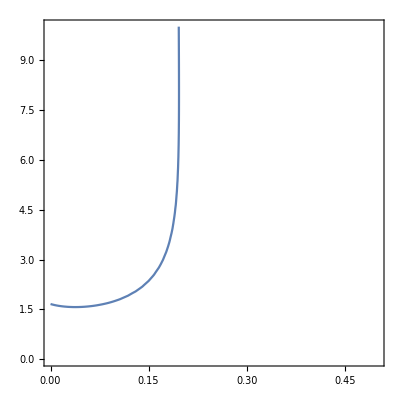

```mathematica
ContourPlot[CascadeNode2[z, r]==0, {r, 0, 0.5}, {z,0,10}]
```

```mathematica
CascadeEdge2[z_, r_] = (SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],2])
```

-((ⅇ^-z (1) (1))/933262154439441526816992388562667004907159682643816214685929638952175999932299156089414639761565182862536979208272237582511852109168640000000000000000000000)+(-1+99+1/37330481430000000)^2
 |  |  |  |

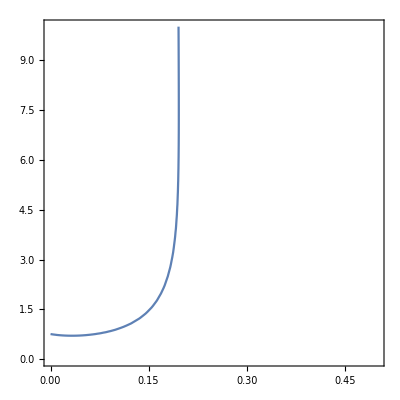

```mathematica
ContourPlot[CascadeEdge2[z, r]==0, {r, 0, 0.5}, {z,0,10}]
```

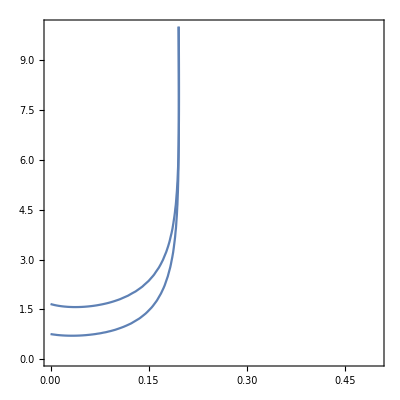

```mathematica
Show[%35, %38]
```

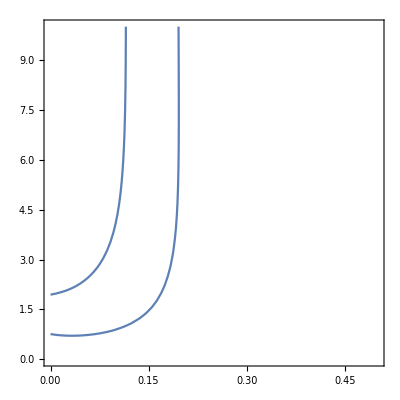

```mathematica
Show[%38, %28]
```

```mathematica
FindRoot[CascadeEdge2[z, 0.371]==0, {z, 4}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{z→1.92563}

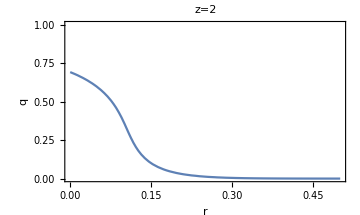

```mathematica
ContourPlot[GN1gauss[q, q, 2, r]==q , {r, 0, 0.5},  {q, 0, 1}, ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z2.eps",%172,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z2.eps

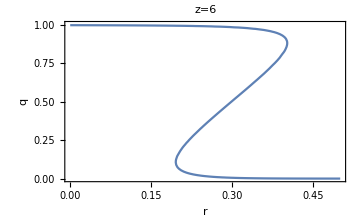

```mathematica
ContourPlot[GN1gauss[q, q, 6, r]==q , {r, 0, 0.5},  {q, 0, 1}, ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=6]]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z6.eps",%173,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z6.eps

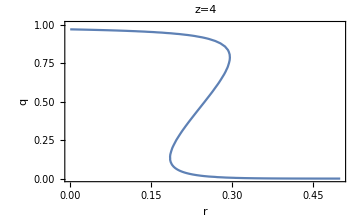

```mathematica
ContourPlot[GN1gauss[q, q, 4, r]==q , {r, 0, 0.5},  {q, 0, 1}, ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=4]]
```

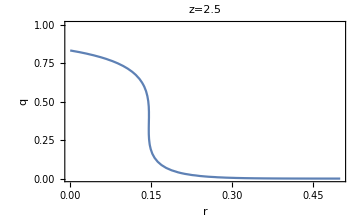

```mathematica
ContourPlot[GN1gauss[q, q, 2.5, r]==q , {r, 0, 0.5},  {q, 0, 1}, ImageSize->{360,215},AspectRatio->Full, FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=2.5]]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z25.eps",%179,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/two_layer_node_qr_z25.eps